```mathematica
ClearAll["Global`*"]
```

```mathematica
(* For the prereheting scenario with inflaton potential , 
(1) we study analytically the inflaton field, daughter mode function  and number density  for different momentum  , neglecting the universe expansion,
showing the equivalence with the Mathieu equation. 
(2)Then, we compute the mode function and number density for a fixed  in which the dynamics presents resonance. This is checked looking at the stability/instability chart. *)
```

## Background equations

```mathematica
(* Background equations: EOM Inflaton field, Friedman equation *)
H[ϕ_,dϕ_]:=√(1/(3 Mpl^2)(1/2 dϕ^2 + 1/2 mϕ^2 ϕ^2));
eqa = a'[t]==a[t]*H[ϕ[t],ϕ'[t]];
eqϕ=ϕ''[t]+mϕ^2 ϕ[t]==0;

(*Initial conditions*)
backgroundconditions = {a[0]==1,ϕ[0]==Φ,ϕ'[0]==0};

(* Solve Background dynamic *)
solbackground=DSolve[{eqϕ,eqa,backgroundconditions[[1]],backgroundconditions[[2]],backgroundconditions[[3]]},{ϕ[t],a[t]},t];

(* Solution's background *)
ϕsol[t_]=Simplify[ϕ[t]/. solbackground[[1]]];
asol[t_]=Simplify[a[t]/. solbackground[[1]]];
```

## Daughter dynamic:

```mathematica
(* Frequency *)
ω2[t_]:=k^2+g^2 ϕsol[t]^2;
ω[t_]:=√ω2[t];

(* EOM daughter χ *)
eqχ=χ''[t]+ω2[t]*χ[t]==0;

(*Initial conditions*)
χconditions={χ[0]==1/(√(2ω[0])),χ'[0]==-I*√(ω[0]/2)}; (* Initial conditions  to be valued at  *)

(*Solve χ dynamic *)
solχ=DSolve[{eqχ,χconditions[[1]],χconditions[[2]]},χ[t],t];

(* Spectator solution *)
χsol[t_]=Simplify[χ[t] /. solχ[[1]]];

(* Number particles *)
numbχ[t_]=1/2 Abs[χsol'[t]]^2/ω[t]+ω[t]/2 Abs[χsol[t]]^2-1/2 //Simplify;
```

## Check equivalence with Mathieu equation:

```mathematica
A[k_] := k^2/mϕ^2+2(g^2 Φ^2)/(4 mϕ^2);

eqnχMathieu=χ''[z]+(A[k]-2*(g^2 Φ^2)/(4 mϕ^2)*Cos[2*z])*χ[z]==0;

ωMathieu[z_,k_]:=Sqrt[A[k]-2*(g^2 Φ^2)/(4 mϕ^2)*Cos[2*z]];

(* Initial condition at z=0 *)
χin[k_]:=1/(√(2 ωMathieu[0,k]));
dχin[k_]:=-I*√(ωMathieu[0,k]/2);

(* Solve *)
solχMathieu=DSolve[{eqnχMathieu,χ[0]==χin[k],χ'[0]==dχin[k]},χ[z],z];

(* Solution *)
χsolMathieu[z_]=Simplify[χ[z]/. solχMathieu[[1]]];
```

## Specific values

```mathematica
Mpl=1.0;                    (* reduced mass Planck *)
mϕ=1.0;                      (* inflation mass *)
g=200.0;                    (* coupling constant ϕ-χ *)
k=1.0;                        (* comoving momentum for χ *)
tMax=50.0;               (* Time *)
Φ=0.1 Mpl;                (* Initial amplitude ϕ *)
```

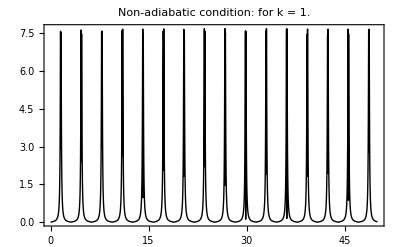

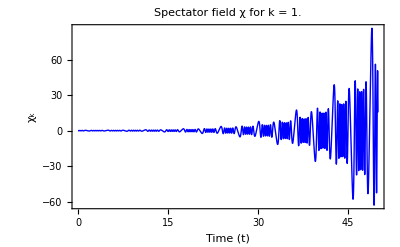

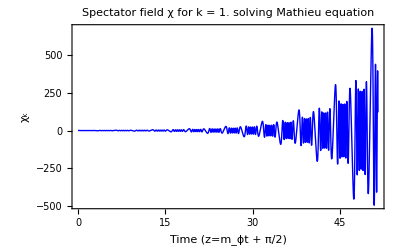

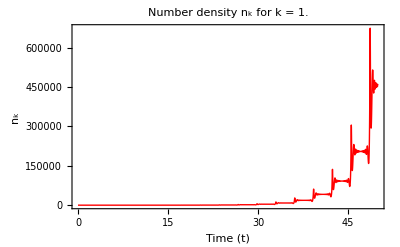

```mathematica
(*Plots *)
Plot[ Abs[ω'[t]]/ω2[t],{t,0,tMax},PlotRange->All,PlotStyle->{Thick,Black},Frame->True,PlotLabel->Style[StringForm["Non-adiabatic condition:  for k = ``",k],12]]

Plot[Re[χsol[t]],{t,0,tMax},PlotRange->All,PlotStyle->{Thick ,Blue},Frame->True,FrameLabel->{"Time (t)","χ_k"},PlotLabel->Style[StringForm["Spectator field χ for k = ``",k],12]]

Plot[Re[χsolMathieu[z]],{z,0,mϕ*tMax + π/2},PlotRange->All,PlotStyle->{Thick ,Blue},Frame->True,FrameLabel->{"Time (z=m_ϕt + π/2)","χ_k"},PlotLabel->Style[StringForm["Spectator field χ for k = `` solving Mathieu equation",k],12]]

Plot[numbχ[t],{t,0,tMax},PlotRange->All,PlotStyle->{Thick,Red},Frame->True,FrameLabel->{"Time (t)","n_k"},PlotLabel->Style[StringForm["Number density n_k for k = ``",k],12]]
```

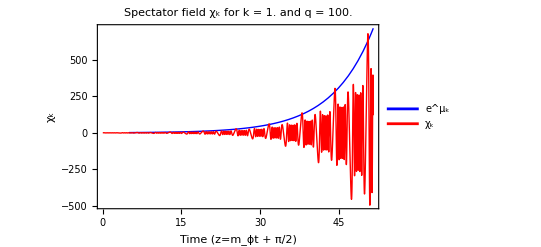

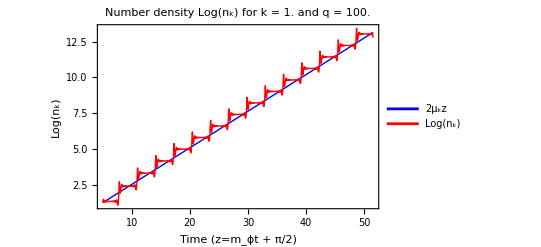

```mathematica
(* Map to Mathieu equation *)
qvalue = (g^2 Φ^2)/(4 mϕ^2);
Avalue = k^2/mϕ^2+2qvalue;
μExp = Abs[Im[MathieuCharacteristicExponent[Avalue,qvalue]]];

χplot = Plot[Re[χsolMathieu[z]],{z,0,mϕ*tMax + π/2},PlotRange->All,PlotStyle->{Thick,Red},PlotLegends->{"χ_k"},Frame->True];
χμplot = Plot[Exp[μExp*z],{z,5,mϕ*tMax+ π/2},PlotRange->All,PlotStyle->{Thick,Blue},PlotLegends->{"e^μ_k"},Frame->True];
Show[χμplot,χplot,FrameLabel->{"Time (z=m_ϕt + π/2)","χ_k"},PlotLabel->Style[StringForm["Spectator field χ_k for k = `` and q = ``",k,qvalue],12]]


nplot = Plot[Log[numbχ[z]],{z,5,mϕ*tMax + π/2},PlotRange->All,PlotStyle->{Thick,Red},PlotLegends->{"Log(n_k)"},Frame->True];
nμplot = Plot[2*μExp*z,{z,5,mϕ*tMax+ π/2},PlotRange->All,PlotStyle->{Thick,Blue},PlotLegends->{"2μ_kz"},Frame->True];
Show[nμplot,nplot,FrameLabel->{"Time (z=m_ϕt + π/2)","Log(n_k)"},PlotLabel->Style[StringForm["Number density Log(n_k) for k = `` and q = ``",k,qvalue],12]]
```

## Stability / Instability chart

Chosen values: q = 100. , A = 201.

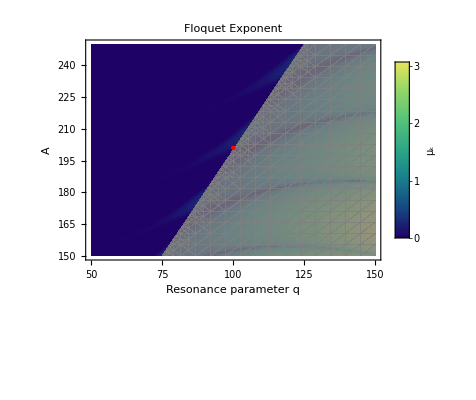

```mathematica
qMaxChart=150;
AMaxChart=250;

μ[A_,q_]:=Abs[Im[MathieuCharacteristicExponent[A,q]]];

plotFloquet=DensityPlot[μ[A,q],{q,50,qMaxChart},{A,150,AMaxChart},PlotPoints->80,MaxRecursion->2,ColorFunction->"BlueGreenYellow",PlotRange->All,PlotLegends->BarLegend[Automatic,LegendLabel->"μ_k"],FrameLabel->{"Resonance parameter q","A"},PlotLabel->"Floquet Exponent"];
unphysicalRegion=RegionPlot[A<2*q,{q,50,qMaxChart},{A,150,AMaxChart},BoundaryStyle->None,PlotStyle->Directive[Gray,Opacity[0.8]]];
PointK = ListPlot[{{qvalue,Avalue}},PlotStyle->{Red,PointSize[Large]}];

Print["\n Chosen values: q = ",qvalue," , A = ",Avalue]
Show[plotFloquet,PointK,unphysicalRegion,Epilog->Text[Style["Unphysical (k^2 < 0)",Black,Bold,14],{qMaxChart*0.7,qMaxChart*0.7}]]
```